Neural Network Computation

## The Example Network

```mathematica
labels = {{1,1}};
x = {{1,1}};
W0 = {{1,-0.5},{-0.5,1}}; 
W1 = {{-2,-2}, {1, -2}}; 
b1 = {-0.5, -1};
b2 = {0,-0.5};
```

-Graphics-

Example Feed-Forward Neural network with initialized weights.

## Hidden and Output Unit Activations

```mathematica
S[x_]:= 1/(1 + E^(-x));
Plot[S[x], {x,-10,10}];
```

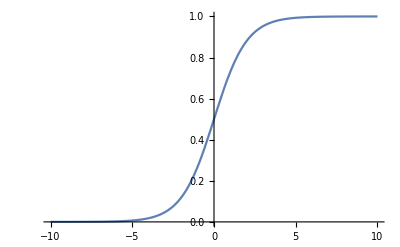

Sigmoid activation function

## First Layer Computations

```mathematica
z0 = Transpose[W0].Transpose[x] + b1;
a0 = S[z0];
```

(0.
-0.5)

z_0 = W_0^T x + b_1

(0.5
0.377541)

a_0 = S(z_0)

## Second Layer Computations

```mathematica
z1 = Transpose[W1].a0 + b2;
a1 = LogisticSigmoid[z1];
```

(-0.622459
-2.25508)

z0 = W_1^T a_0 + b_2

(0.349222
0.0949121)

a_1 = S(z_1)

## Error

```mathematica
Err = RootMeanSquare[(Transpose[a1] - y)]^2;
```

(0.423512
0.819184)

Err = ∑_i (a_(1_i)- (y_i))^2

## Derivatives

(∂E)/(∂a_1) = (a_1- y)

(∂a_1)/(∂z_1) = S(z_1) * (1-S(z_1))

(∂z_1)/(∂W_1) = a_0

(∂z_1)/(∂b_2) = 1

(∂z_1)/(∂a_0) = W_1

(∂a_0)/(∂z_0) = S(z_0) * (1-S(z_0))

(∂z_0)/(∂W_0) = x

(∂z_0)/(∂b_1) = 1

```mathematica
dEa1 = (Transpose[y] - a1);
da1z1 = S[z1] * (1-S[z1]);
dz1W1 = a0;
dz1b2 = 1;
dz1a0 = W1;
da0z0 = S[z0] * (1-S[z0]);
dz0W0 = x;
dz0b1 = 1;
```

(∂E)/(∂W_1) =(∂E)/(∂a_1)*(∂a_1)/(∂z_1)⊗(∂z_1)/(∂W_1)

(∂E)/(∂b_2) =(∂E)/(∂a_1)*(∂a_1)/(∂z_1)*(∂z_1)/(∂b_2)

(∂E)/(∂W_0) =(∂E)/(∂a_1)*(∂a_1)/(∂z_1)*(∂z_1)/(∂a_0)* (∂a_0)/(∂z_0)⊗(∂z_0)/(∂W_0)

(∂E)/(∂b_1) =(∂E)/(∂a_1)*(∂a_1)/(∂z_1)*(∂z_1)/(∂a_0)* (∂a_0)/(∂z_0)*(∂z_0)/(∂b_1)

```mathematica
dEW1 = Outer[Times, ArrayReshape[dEa1*da1z1, {2}], ArrayReshape[Transpose[dz1W1],{2}]];
dEb2 = dEa1*da1z1*dz1b2;
dEW0 = Outer[Times, ArrayReshape[dz1a0.dEa1*da1z1*da0z0, {2}], ArrayReshape[dz0W0,{2}]];
dEb1 = dz1a0.dEa1*da1z1*da0z0*dz0b1;
```

(0.0739498 | 0.0558382
0.0388752 | 0.029354)

(∂E)/(∂W_1)

(0.1479
0.0777505)

(∂E)/(∂b_2)

(-0.176798 | -0.176798
-0.0234056 | -0.0234056)

(∂E)/(∂W_0)

(-0.176798
-0.0234056)

(∂E)/(∂b_1)

## Weight Updates

η = 0.1

Δ_w_1= -η(∂E)/(∂W_1)

Δ_b_2= -η(∂E)/(∂b_2)

Δ_w_0= -η(∂E)/(∂W_0)

Δ_b_1= -η(∂E)/(∂b_1)

```mathematica
n = 0.1;
W1 = W1 - n*dEW1;
b2 = b2 - n*dEb2;
W0 = W0 - n*dEW0;
b1 = b1 - n*dEb1;
```

(-2.00739 | -2.00558
0.996112 | -2.00294)

W_1

(-0.01479
-0.507775)

b_2

(1.01768 | -0.48232
-0.497659 | 1.00234)

W_0

(-0.48232
-0.997659)

b_1

Kim Hammar

kimham@kth.se

2/1 - 2018